Corso di Laboratorio Computazionale — Corso di Laurea in Matematica — Università di Padova.

Anno Accademico 2019-2020

# Esercizi 2. Crittografia

Notebook del gruppo Cammelli Tonanti.
Componenti del gruppo: Francesco Tognetti, Riccardo Cazzin.
Se ci sono stati collaborazioni o aiuti al di fuori del gruppo, dichiararli.
In collaborazione con
Aiutati da

## Esercizio 2.1 (Decrittazione di messaggio (Hill)).

### Testo dell’esercizio

Il messaggio

"WWMGuuuqkYUFwYcWV'.YryomxpQvkfmzaqqpKQEtUpWKES.ZArynoXGDqrymGOeQEvkfmzaqqpKQEtUpWKEtCuoXPqqYxiqZAKEaDocjVKseHV' WPtCTC'.KKzxranoXGDqKEuuWWcQXPxGpKfvxGEVKEtzJyaDTUxGEV' sCeExwNbrvkluKEuuGG' alAhqraryhqKEuuGGLXcYncCCgapQncDqyouq; aXGOqkkGGgaGfOl; IJyaDqWqWrymGOeQE; aXGOqkk' alAhqraM.wTTRWkuuMGuuGGMGqqTUsgfRJyITUFOqqqWnTXqTtwwNTXncCCpyKETXryo UFKErjkkgLLmwT'' xvncqmyomxpQOqqqWnTXryqqpyQEVtqT; UEbxvkkWnTXuuTUvkfmzaqqpKQErynoXGDqyoYoBFvklutUv' kkIZJyKErjkkgLdS`mevQEFlKK.`kI; U.lhRUtaD"

è stato prima codificato in una lista di numeri, poi crittato con Hill ed infine decodificato e ritrasformato in una stringa. La codifica/decodifica iniziale e finale utilizza i seguenti codici numerici per i seguenti 58 caratteri, che includono tutte le lettere minuscole e maiuscole e altri sei caratteri:

Carattere | ASCII | Codice usato
A, …, Z | 65, …, 90 | 1, …, 26 (ASCII - 64)
a, …, z | 97, …, 122 | 33, …, 58 (ASCII - 64)
. | 46 | 27
, | 44 | 28
spazio | 32 | 29
` | 96 | 30
' | 39 | 31
; | 59 | 32

La crittazione alla Hill è stata fatta usando una matrice intera 2×2 invertibile in ℤ_58. Ci sono circa 12 milioni di tali matrici (scritte a coefficienti in ℤ_58) e di esse oltre 4 milioni  sono invertibili in ℤ_58. Questo è un numero troppo alto per provare a decrittare il messaggio con tutte. Però si sa che il messaggio è stato crittato usando una matrice invertibile in ℤ_58 il cui determinante è congruo a 1 (mod 58) e ci sono “solo” 146160 tali matrici.

### Svolgimento

Innanzitutto assegniamo il messaggio ad una variabile.

```mathematica
messaggio="WWMGuuuqkYUFwYcWV'. YryomxpQvkfmzaqqpKQEtUpWKES.ZArynoXGDqrymGOeQEvkfmzaqqpKQEtUpWKEtCuoXPqqYxiqZAKEaDocjVKseHV'WPtCTC'.KKzxranoXGDqKEuuWWcQXPxGpKfvxGEVKEtzJyaDTUxGEV'sCeExwNbrvkluKEuuGG'alAhqraryhqKEuuGGLXcYncCCgapQncDqyouq;aXGOqkkGGgaGfOl;IJyaDqWqWrymGOeQE;aXGOqkk'alAhqraM.wTTRWkuuMGuuGGMGqqTUsgfRJyITUFOqqqWnTXqTtwwNTXncCCpyKETXryo UFKErjkkgLLmwT''xvncqmyomxpQOqqqWnTXryqqpyQEVtqT;UEbxvkkWnTXuuTUvkfmzaqqpKQErynoXGDqyoYoBFvklutUv'kkIZJyKErjkkgLdS`mevQEFlKK.`kI;U.lhRUtaD";
```

Controlliamo, poi, che la stringa ricevuta abbia un numero pari di caratteri, così da rendere più agevole la decrittazione in seguito.

```mathematica
StringLength@messaggio//EvenQ
```

Creiamo una funzione che converta le stringhe nel sistema a cinquantotto caratteri richiesto. Benché non sia necessariamente l’approccio più elegante, decidiamo di sottrarre 64 dal codice ASCII di tutti i caratteri e di aggiustare con regole di sostituzione adeguate i caratteri non alfabetici.

```mathematica
stringaAdNumeri[str_]:=(
ToCharacterCode[str]-64
)/.{
46-64->27,(*punto*)
44-64->28,(*virgola*)
32-64->29,(*spazio*)
96-64->30,(*accento grave*)
39-64->31,(*apostrofo / accento acuto*)
59-64->32 (*punto e virgola*)
}
```

Analogamente, ne scriviamo anche la funzione inversa. Poiché le regole di sostituzione sono formalmente espressioni del tipo Rule[expr1, expr2], usiamo Reverse per non doverle riscrivere a rovescio manualmente.

```mathematica
numeriAdStringa[l_]:=FromCharacterCode[
(
(
l/.Reverse/@{
46-64->27,(*punto*)
44-64->28,(*virgola*)
32-64->29,(*spazio*)
96-64->30,(*accento grave*)
39-64->31,(*apostrofo / accento acuto*)
59-64->32 (*punto e virgola*)
}
)/.{0->58}(*z*)
)+64
]
```

Scriviamo una funzione che divida in coppie la lista di numeri creata dalla trasformazione da stringhe a numeri. Non dobbiamo preoccuparci di gestire il caso in cui la stringa abbia un numero dispari di caratteri, perché messaggio è di lunghezza pari.

```mathematica
coppie[l_]:=Partition[l,2]
```

```mathematica
mes0=messaggio//stringaAdNumeri//coppie;
```

Generiamo tutte le matrici di ℤ_58 ed estraiamo quelle di determinante congrue a 1 mod 58: per le proprietà del determinante, infatti, il fatto che la chiave privata abbia determinante congruo 1 mod 58 implica che anche la sua inversa abbia determinante congruo a 1 mod 58.

```mathematica
chiavi=Select[Tuples[Range[0,57],{2,2}],Det[#,Modulus->58]==1&];
```

Effettivamente ci sono 146160 chiavi.

```mathematica
Length@chiavi
```

Creata una funzione di sostegno per applicare la matrice a tutte le coppie di una lista, generiamo tutte le possibili decrittazioni.

```mathematica
scalare[matrice_,lista_]:=matrice.#&/@lista
```

```mathematica
possibili=Flatten/@Mod[Map[scalare[#,mes0]&,chiavi],58];
```

Le decrittazioni possibili sono troppe per poterle controllare manualmente: occorre, dunque, un criterio con cui controllarne solo una piccola parte. Cominciamo visualizzando la quantità di lettere minuscole presenti nelle decrittazioni possibili. Per vedere il numero esatto di casi per ogni barra, è sufficiente porre la freccia del mouse sopra tale barra.

```mathematica
Histogram[Count[#,a_/;33≤a≤58]&/@possibili]
```

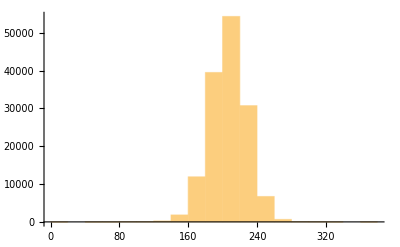

Come si può notare mettendo la freccia del mouse a ridosso dell’asse x, ci sono davvero poche stringhe che abbiano più di 300 caratteri minuscoli. Un primo apporccio, quindi, può consistere nel controllare le stringhe in base a quanti caratteri minuscoli contengono. Controlliamo se la stringa con più caratteri minuscoli è quella giusta.

```mathematica
massimo=Max[Count[#,a_/;33≤a≤58]&/@possibili];
sequenza=Select[possibili,Count[#,a_/;33≤a≤58]==massimo&];
```

```mathematica
sequenza//First//numeriAdStringa
```

Ora troviamo la matrice che è stata usata per decrittare il messaggio ed invertiamola, in modo da ottenere la chiave privata usata inizialmente.

```mathematica
Position[possibili,%15//First]
```

```mathematica
Inverse[chiavi⟦131594⟧,Modulus->58]
```